# Artillery Aim Simulator

## Collin Davis and Chandler Jensen

## General Information:

I believe the easiest way to go about this project is to pick an artillery weapon currently in use by the United States military and use it for our simulation. Perhaps if we were to continue the project beyond the class we could add different weapons and allow the user to pick, but let’s not get ahead of ourselves.

Wikipedia has some good info on different artillery weapons, I think the M777 Howitzer is a good choice, coupled with the 155mm M795 shell. It has the following specifications (according to Wikipedia):
Range of Elevation: 0° - +71.7°
Muzzle Velocity: 827 m/s
Effective Firing Range: 22.5km

## Global Variables:

```mathematica
V0=827; (* V0 is the initial velocity of the shell *)
maxRange=22500; (* maximum range of the cannon *)
minRange=100 ;(* I decided to set the minimum range at 100 meters - anything closer, use different weapons *)
elevationMin=0Degree; (* minimum angle between horizontal plane and cannon *)
elevationMax=71.7Degree; (* maximum angle between horizontal plane and cannon *)
```

## Random Conditions Generator:

### Wind Generation

{-0.109613,-0.808738}

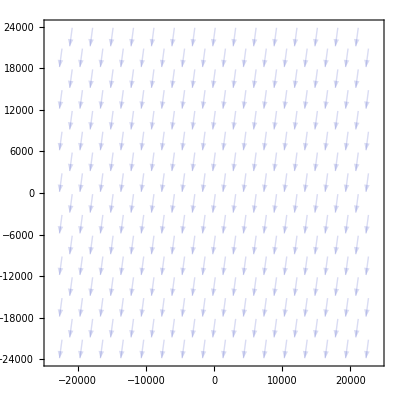

```mathematica
windSpeed=RandomReal[{0,20}];
(* I chose 20 m/s as the maximum windspeed as the Beaufort wind scale classifies this windspeed as "Gale" *)
windDirection=RandomReal[{0,2π}];
windVector=AngleVector[{windSpeed,windDirection}]
windPlot=VectorPlot[windVector,{x,-maxRange,maxRange},{y,-maxRange,maxRange},VectorStyle->Opacity[0.15]]
```

### Target Location Generation

{8835.2,6049.77}

{0,0}

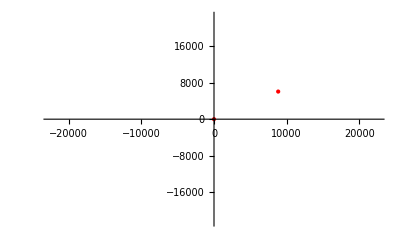

```mathematica
targetPosition={RandomReal[{minRange,maxRange}],RandomReal[{minRange,maxRange}]} (* TODO create While loop that continues to find random numbers while ||targetposition|| > maxRange || < minRange *)
artilleryPosition={0,0}
positionPlot=ListPlot[{targetPosition,artilleryPosition},AxesOrigin->{0,0},PlotRange->{{-maxRange,maxRange},{-maxRange,maxRange}},PlotStyle->{Red,PointSize[Large]}]
```

```mathematica
{6975.5284541412875,8659.868217724943}
```

{6975.53,8659.87}

### Combined Conditions

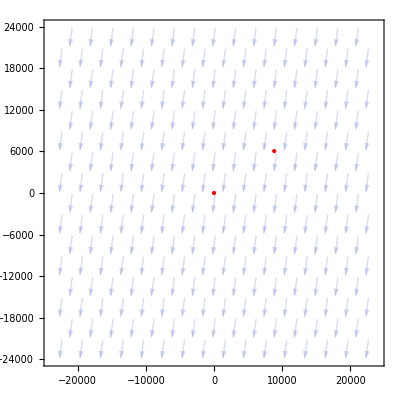

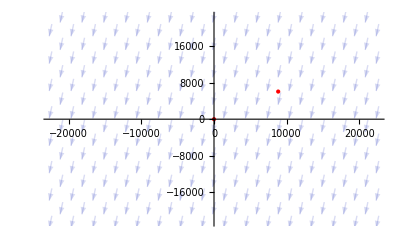

```mathematica
Graphics[{Thick,Blue,Arrow[{{0,0},windVector}]}];
Show[windPlot,positionPlot]
Show[positionPlot,windPlot]
```